# Beliefs: a catalyst for cooperation

## Evolutionary dynamics in infinite populations

## Brief description

In total there are eight different strategies.The strategies can be enumerated by the generic profile (a_1^*,a_2^*,u^*)where a_i^* is the hunting strategy of the focal individual when in reality i and  u^* is the preferred reality of the focal individual (objective or inter-subjective).The individuals in the tribe form a group of size G and first they need to decide which reality they choose to believe in.

### Definitions and variables that will be used

there are eight possible strategies as defined by (a_1^*,a_2^*,u^*), since there are two action in each reality i so

```mathematica
Subscript[x, 1]=Subscript[x, hh1]+Subscript[x, hs1]+Subscript[x, sh1]+Subscript[x, ss1];
Subscript[x, 2]=Subscript[x, hh2]+Subscript[x, hs2]+Subscript[x, sh2]+Subscript[x, ss2];
```

Let us define the strategies and give them colors - This is how we will identify strategies later.

```mathematica
freqnotation={Subscript[x, hh1],Subscript[x, hh2],Subscript[x, hs1],Subscript[x, hs2],Subscript[x, sh1],Subscript[x, sh2],Subscript[x, ss1],Subscript[x, ss2]};
colors={RGBColor["#B22222"],RGBColor["#DC143C"],RGBColor["#FF4501"],RGBColor["#00BFBF"],RGBColor["#6495ED"],RGBColor["#F08080"],RGBColor["#02008B"],RGBColor["#008B8B"]};
```

```mathematica
PieChart[{1/8,1/8,1/8,1/8,1/8,1/8,1/8,1/8},SectorOrigin->{Automatic,2},ChartStyle->colors⟦{1,3,2,4,7,8,5,6}⟧,ChartLabels->Placed[Style[ToString[#],White,14]&/@{1,2,1,2,1,2,1,2},"RadialCenter"]]
```

-Graphics-

Group size if G of which M is the minimum number of stag hunters required to bring down a stag.  The nutritional worth of a hare is set to πH while that of a stag is πS.

```mathematica
G=5;M=4;πS=4;πH=1;
```

## All calculations done here (compile this)

#### Group decides on how to define reality

```mathematica
f1[k_,state_]:=(*0.5*)(k+KroneckerDelta[state,1])/G(*Round[(k+KroneckerDelta[state,1])/G]*);
```

The function f_1(k,state) returns the probability of group G choosing reality 1. The probability is a frequency dependent function

#### What is an individuals behaviour? Hare hunting or stag hunting?

```mathematica
Phare1[focal_]:=KroneckerDelta[focal,"Hare"];
```

This function returns “Hare” if the focal individual is a hare hunter for a given reality.

#### What is the group composition?

What is the composition of the group? How many stag hunters are there?given that k of the group believe in reality 1 and the rest in reality 2

```mathematica
Pcomposition[k_,state_]:=(∑_(l=0)^k ∑_(m=0)^k ∑_(n=0)^k ∑_(o=0)^k ∑_(p=0)^(G-1-k) ∑_(q=0)^(G-1-k) ∑_(r=0)^(G-1-k) ∑_(s=0)^(G-1-k) (If[l+m+n+o==k&&p+q+r+s==G-1-k,Multinomial[l,m,n,o] Multinomial[p,q,r,s](Subscript[x, hh1])^l(Subscript[x, hs1])^m(Subscript[x, sh1])^n(Subscript[x, ss1])^o(Subscript[x, hh2])^p(Subscript[x, hs2])^q(Subscript[x, sh2])^r(Subscript[x, ss2])^s If[state==1,HeavisideTheta[1+n+o+r+s-M],If[state==2,HeavisideTheta[1+m+o+q+s-M],0]],0]));
```

#### Calculating the average payoffs

What is the composition of the group? How many stag hunters are there? given that k of the group believe in reality 1 and the rest in reality 2

Simplified version of the average payoffs

```mathematica
avgpayoffsimplified[focal1_,focal2_,state_]:=πH (Phare1[focal1]∑_(k=0)^(G-1) (Binomial[G-1,k] (Subscript[x, 1])^k(Subscript[x, 2])^(G-1-k)f1[k,state])+Phare1[focal2]∑_(k=0)^(G-1) (Binomial[G-1,k] (Subscript[x, 1])^k(Subscript[x, 2])^(G-1-k)(1-f1[k,state])))+πS((1-Phare1[focal1])∑_(k=0)^(G-1) (Binomial[G-1,k] f1[k,state] Pcomposition[k,1])+(1-Phare1[focal2])∑_(k=0)^(G-1) (Binomial[G-1,k] (1-f1[k,state])  Pcomposition[k,2]));
```

The average payoffs are stored in a table called payoffstab:

```mathematica
payoffstab=Flatten[Table[{{foc1,foc2,flags},avgpayoffsimplified[foc1,foc2,flags]},{foc1,{"Hare","Stag"}},{foc2,{"Hare","Stag"}},{flags,{1,2}}]/.HeavisideTheta[0]->1,2]//Simplify;
```

In the following we write down the matrix which gives the average payoff of strategy i when playing with strategy j at the i,j entry of the fullreducedmatrix

```mathematica
nullreplace={Subscript[x, hh1]->0,Subscript[x, hh2]->0,Subscript[x, hs1]->0,Subscript[x, hs2]->0,Subscript[x, sh1]->0,Subscript[x, sh2]->0,Subscript[x, ss1]->0,Subscript[x, ss2]->0};
toreplace[pair_]:=nullreplace/.{(freqnotation⟦pair⟦1⟧⟧->0)->freqnotation⟦pair⟦1⟧⟧->y,(freqnotation⟦pair⟦2⟧⟧->0)-> freqnotation⟦pair⟦2⟧⟧->1-y};
reducedmatrix={};
Table[
temp=Table[Drop[Drop[nullreplace,{j}],{i}],{i,1,7,1}];
AppendTo[reducedmatrix,Table[payoffstab⟦j,2⟧/.temp⟦i⟧//Simplify,{i,1,7,1}]],{j,1,8,1}];
diagonals=Table[payoffstab⟦j,2⟧/.Drop[nullreplace,{j}]//Simplify,{j,1,8,1}];
fullreducedmatrix=Table[Insert[reducedmatrix⟦i⟧,diagonals⟦i⟧,i],{i,1,8,1}];
```

#### Calculating fixed points

Next we calculate the fixed points between two strategies at a time and store the results in the array allpairs

```mathematica
allpairs=Table[If[i≠j, freqnotation⟦i⟧/.Solve[freqnotation⟦i⟧>0&&freqnotation⟦i⟧<1&&0==freqnotation⟦i⟧(1-freqnotation⟦i⟧)(fullreducedmatrix⟦i,j⟧-fullreducedmatrix⟦j,i⟧)/.{freqnotation⟦j⟧->1-freqnotation⟦i⟧},freqnotation⟦i⟧,Reals]//N,]//Flatten,{i,1,7,1},{j,i+1,8,1}]//Quiet;
```

Using the above information now we can simply plot the dynamics between any two strategies

#### Prepping the plot package

```mathematica
Pairwiseplot[strat1_,strat2_]:=(eq=freqnotation⟦strat1⟧(1-freqnotation⟦strat1⟧)(fullreducedmatrix⟦strat1,strat2⟧-fullreducedmatrix⟦strat2,strat1⟧)/.{freqnotation⟦strat2⟧->1-freqnotation⟦strat1⟧};
Plot[eq/.{freqnotation⟦strat1⟧->x},{x,0,1},Frame->True,Filling->Axis,FillingStyle->{colors⟦strat2⟧,colors⟦strat1⟧},PlotStyle->Black,FrameStyle->Directive[Black,Thickness[0.002]],FrameLabel->{freqnotation⟦strat1⟧,freqnotation⟦strat1⟧(1-freqnotation⟦strat1⟧)(Subscript[f, freqnotation⟦strat1⟧]-Subscript[f, freqnotation⟦strat2⟧])},ImageSize->Medium]);
```

```mathematica
(*CirclePoints is an alternative to manually generating the vertex list*)pts=CirclePoints[{1,23 Degree},8];
pts={{-Cos[23 °],-Sin[23 °]},{-Cos[23 °-π/4],-Sin[23 °-π/4]},{-Cos[23 °+π/4],-Sin[23 °+π/4]},{Sin[23 °],-Cos[23 °]},{Cos[23 °+π/4],Sin[23 °+π/4]},{-Sin[23 °],Cos[23 °]},{Cos[23 °],Sin[23 °]},{Cos[23 °-π/4],Sin[23 °-π/4]}};
(*Generate all edges and internal diagonals as Line objects*)
lines=Line/@Subsets[pts,{2}];
(*List all possible pairs of lines from the set above*)
linepairs=Subsets[lines,{2}];
(*Find unique intersection points between lines in each pair*)
intersectionpts=DeleteDuplicatesBy[N]@Simplify@DeleteCases[RegionIntersection/@linepairs,_EmptyRegion];
eqpts={};
Table[If[MatchQ[allpairs⟦i,j⟧⟦1⟧,_Real],
AppendTo[eqpts,{pts⟦i⟧⟦1⟧+(1-allpairs⟦i,j⟧⟦1⟧)(pts⟦j+i⟧⟦1⟧-pts⟦i⟧⟦1⟧),pts⟦i⟧⟦2⟧+(1-allpairs⟦i,j⟧⟦1⟧)(pts⟦j+i⟧⟦2⟧-pts⟦i⟧⟦2⟧)}]],{i,1,7,1},{j,1,Length[allpairs⟦i⟧],1}];
eqpts=DeleteCases[eqpts,Null];
eqptsplot=Point[#]&/@eqpts;
```

## Plotting

Simply choose the two strategies you want to see the dynamics of selected strategies, the list below might be useful for coding
1. (x_hh1,RGBColor[0.6980392156862745, 0.13333333333333333, 0.13333333333333333] ); 2.(x_hh2,RGBColor[0.8627450980392157, 0.0784313725490196, 0.23529411764705882]); 3.(x_hs1,RGBColor[1., 0.27058823529411763, 0.00392156862745098]); 4.(x_hs2,RGBColor[0., 0.7490196078431373, 0.7490196078431373]); 5.(x_sh1,RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824]); 6.(x_sh2,RGBColor[0.9411764705882353, 0.5019607843137255, 0.5019607843137255]); 7.(x_ss1,RGBColor[0.00784313725490196, 0., 0.5450980392156862]); 8.(x_ss2,RGBColor[0., 0.5450980392156862, 0.5450980392156862])

```mathematica
Manipulate[Pairwiseplot[i,j],{{i,1,"Strategy"},{1,2,3,4,5,6,7,8}},{{j,4,"against strategy"},{1,2,3,4,5,6,7,8}}]
```

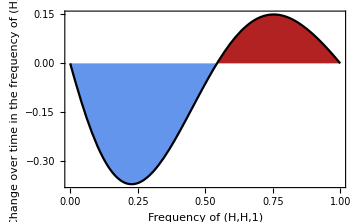

```mathematica
Show[Pairwiseplot[1,5],Frame->True,FrameStyle->Black,FrameLabel->{Style["Frequency of (H,H,1)",14,Black],Style["Change over time in\n the frequency of (H,H,1)",14,Black]}]
```

The dynamics of the whole population takes place in a seven dimensional simplex Δ_7and we can show the dynamics as . (x_hh1,RGBColor[0.6980392156862745, 0.13333333333333333, 0.13333333333333333] ); 2.(x_hh2,RGBColor[0.8627450980392157, 0.0784313725490196, 0.23529411764705882]); 3.(x_hs1,RGBColor[1., 0.27058823529411763, 0.00392156862745098]); 4.(x_hs2,RGBColor[0., 0.7490196078431373, 0.7490196078431373]); 5.(x_sh1,RGBColor[0.39215686274509803, 0.5843137254901961, 0.9294117647058824]); 6.(x_sh2,RGBColor[0.9411764705882353, 0.5019607843137255, 0.5019607843137255]); 7.(x_ss1,RGBColor[0.00784313725490196, 0., 0.5450980392156862]); 8.(x_ss2,RGBColor[0., 0.5450980392156862, 0.5450980392156862])

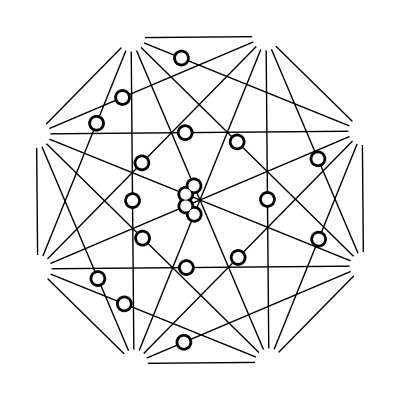

```mathematica
Graphics[{lines,Black,PointSize[0.03],eqptsplot,White,PointSize[0.02],eqptsplot,PointSize[0.05],Point[pts,VertexColors->colors]}]
```